二维实矩阵

0

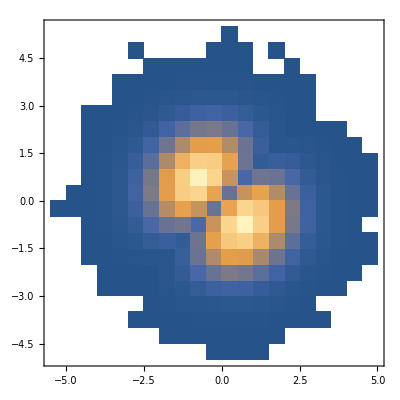

```mathematica
Clear["Global`*"]
P[λ1_,λ2_]:=Abs[λ1-λ2]*Exp[-(λ1^2+λ2^2)]/4 √π
num=500000;
res=RandomSample/@Eigenvalues/@RandomVariate[GaussianOrthogonalMatrixDistribution[2],num];
(*nd表示网格数,num表示数据点总数*)
x1left=-4.0;x1right=4.0;x2left=-4.0;x2right=4.0;
(*x1left=-2.0;x1right=2.0;x2left=-2.0;x2right=2.0;*)
nd=40;  
dx1=(x1right-x1left)/nd;dx2=(x2right-x2left)/nd;
dis=Table[{x1left+i*dx1,x2left+j*dx2,0},{i,1,nd},{j,1,nd}];
Length[x1]


res=RandomSample/@res;(*这个很关键，因为在求解特征值时，人为指定λ1,λ2；也可以是λ2,λ1，进行随机抽样以弥补求解时的漏洞*)



x1=res[[All,1]];x2=res[[All,2]];
DensityHistogram[res]
(*对超过边界的结果，放到边界上，对总结果分布不影响*)
Do[
If[(Abs[x1[[i]]]-Abs[x1left+dx1])>=0,x1[[i]]=x1left+dx1];
If[(Abs[x2[[i]]]-Abs[x2left+dx2])>=0,x2[[i]]=x2left+dx2],
{i,Length[x1]}]
(*转化为概率密度*)
Do[
dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[3]]=dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[3]]+1,
{i,Length[x1]}]
Do[
Do[
dis[[i,j,3]]=dis[[i,j,3]]/num/(dx1*dx2),{j,nd}],{i,nd}];
```

```mathematica
{ListPointPlot3D[dis,PlotRange->All],ListPlot3D[Flatten[dis,1],PlotRange->All,PlotTheme->"Classic"]}
```

{-Graphics3D-,-Graphics3D-}

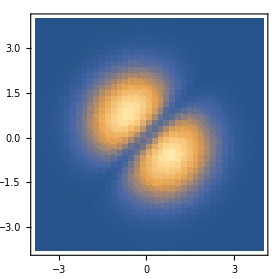

```mathematica
ListDensityPlot[Flatten[dis,1],PlotRange->All]
```

(ⅇ^(1/2 (-λ1^2-λ2^2)) Abs[-λ1+λ2])/(4 √π)

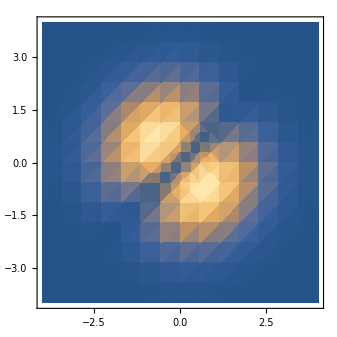
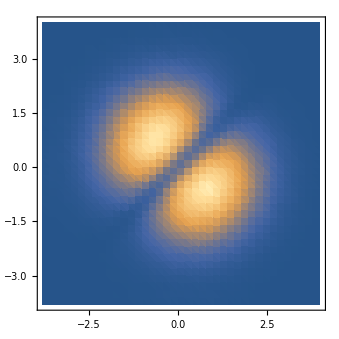

-Graphics3D-

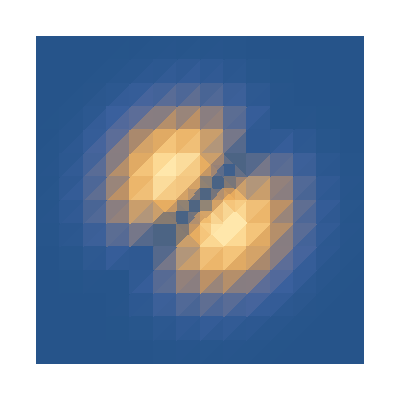

-Graphics3D-

```mathematica
LevelDistribution[n_Integer,β_]:=ProbabilityDistribution[1/(2π)^(n/2)(∏_j^n Gamma[1+β/2]/Gamma[1+(β j)/2])(∏_(i=1)^n ∏_j^(i-1) Abs[Subscript[λ, i]-Subscript[λ, j]]^β)Exp[-1/2∑_(i=1)^n Subscript[λ, i]^2],Array[{Subscript[λ, #],-∞,∞}&,n,1,Sequence]]
pdf=PDF[LevelDistribution[2,1],{λ1,λ2}]

{DensityPlot[pdf,{λ1,-4,4},{λ2,-4,4},PlotRange->All],ListDensityPlot[Flatten[dis,1],PlotRange->All]}
Show[ListPointPlot3D[dis,PlotRange->All],
Plot3D[pdf,{λ1,-4,4},{λ2,-4,4},PlotStyle->None,MeshStyle->Thick,PlotRange->All]]
DensityPlot[pdf,{λ1,-4,4},{λ2,-4,4},PlotTheme->"Minimal",PlotRange->All]
Show[ListPlot3D[Flatten[dis,1],PlotRange->All,PlotTheme->"Classic"],Plot3D[pdf,{λ1,-4,4},{λ2,-4,4},PlotStyle->None,MeshStyle->Thick,PlotRange->All]]
```

二维复矩阵

0

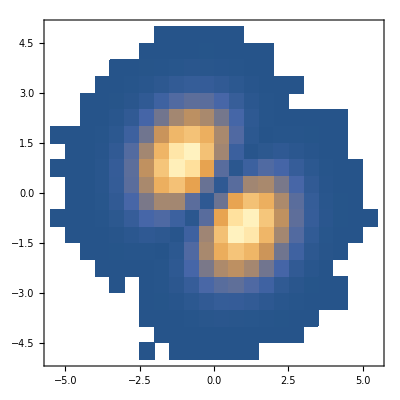

```mathematica
Clear["Global`*"]
P2C[λ1_,λ2_]:=Abs[λ1-λ2]^2*Exp[-(λ1^2+λ2^2)/2]
P2[λ1_,λ2_]:=Abs[λ1-λ2]*Exp[-(λ1^2+λ2^2)/2]
num=500000;

res=RandomSample/@Eigenvalues/@RandomVariate[GaussianUnitaryMatrixDistribution[2],num];
(*nd表示网格数,num表示数据点总数*)
x1left=-4.0;x1right=4.0;x2left=-4.0;x2right=4.0;
(*x1left=-2.0;x1right=2.0;x2left=-2.0;x2right=2.0;*)
nd=40;  
dx1=(x1right-x1left)/nd;dx2=(x2right-x2left)/nd;
dis=Table[{x1left+i*dx1,x2left+j*dx2,0},{i,1,nd},{j,1,nd}];
Length[x1]


res=RandomSample/@res;(*这个很关键，因为在求解特征值时，人为指定λ1,λ2；也可以是λ2,λ1，进行随机抽样以弥补求解时的漏洞*)



x1=res[[All,1]];x2=res[[All,2]];
DensityHistogram[res]
(*对超过边界的结果，放到边界上，对总结果分布不影响*)
Do[
If[(Abs[x1[[i]]]-Abs[x1left+dx1])>=0,x1[[i]]=x1left+dx1];
If[(Abs[x2[[i]]]-Abs[x2left+dx2])>=0,x2[[i]]=x2left+dx2],
{i,Length[x1]}]
(*转化为概率密度*)
Do[
dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[3]]=dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[3]]+1,
{i,Length[x1]}]
Do[
Do[
dis[[i,j,3]]=dis[[i,j,3]]/num/(dx1*dx2),{j,nd}],{i,nd}];
```

```mathematica
{ListPointPlot3D[dis,PlotRange->All],ListPlot3D[Flatten[dis,1],PlotRange->All,PlotTheme->"Classic"]}
Show[Plot3D[P2C[x1,x2]/(4Pi),{x1,-4,4},{x2,-4,4},PlotRange->All,PlotStyle->None,MeshStyle->Thick],ListPlot3D[Flatten[dis,1],PlotRange->All,PlotTheme->"Classic"]]
```

{-Graphics3D-,-Graphics3D-}

-Graphics3D-

(ⅇ^(1/2 (-λ1^2-λ2^2)) Abs[-λ1+λ2]^2)/(4 π)

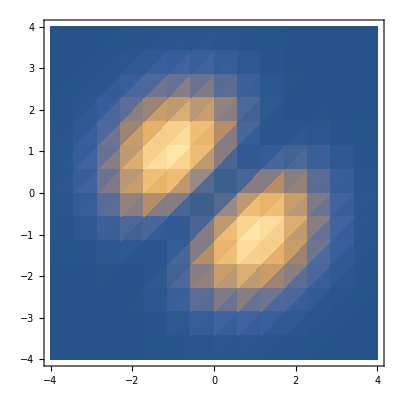
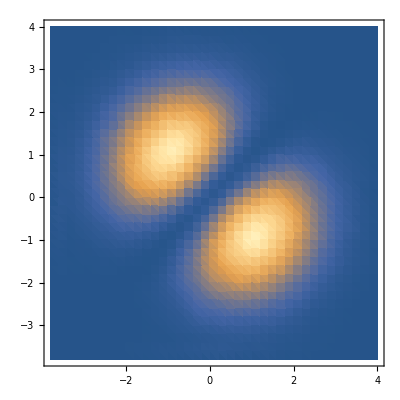

-Graphics3D-

```mathematica
LevelDistribution[n_Integer,β_]:=ProbabilityDistribution[1/(2π)^(n/2)(∏_j^n Gamma[1+β/2]/Gamma[1+(β j)/2])(∏_(i=1)^n ∏_j^(i-1) Abs[Subscript[λ, i]-Subscript[λ, j]]^β)Exp[-1/2∑_(i=1)^n Subscript[λ, i]^2],Array[{Subscript[λ, #],-∞,∞}&,n,1,Sequence]]
pdf=PDF[LevelDistribution[2,2],{λ1,λ2}]
{DensityPlot[pdf,{λ1,-4,4},{λ2,-4,4},PlotRange->All],ListDensityPlot[Flatten[dis,1],PlotRange->All]}
Show[ListPointPlot3D[dis,PlotRange->All],
Plot3D[pdf,{λ1,-4,4},{λ2,-4,4},PlotStyle->None,MeshStyle->Thick,PlotRange->All]]
```

三维实矩阵

```mathematica
Clear["Global`*"]
num=1000000;
x1left=-4.0;x1right=4.0;x2left=-4.0;x2right=4.0;x3left=-4.0;x3right=4.0;
(*x1left=-2.0;x1right=2.0;x2left=-2.0;x2right=2.0;*)
nd=100;  
dx1=(x1right-x1left)/nd;dx2=(x2right-x2left)/nd;dx3=(x2right-x2left)/nd;
dis=Table[{x1left+i*dx1,x2left+j*dx2,x3left+k*dx3,0},{i,1,nd},{j,1,nd},{k,1,nd}];
res=RandomSample/@Eigenvalues/@RandomVariate[GaussianOrthogonalMatrixDistribution[3],num];
x1=res[[All,1]];
x2=res[[All,2]];
x3=res[[All,3]];
(*DensityHistogram[res]*)
(*对超过边界的结果，放到边界上，对总结果分布不影响*)
Do[
If[(Abs[x1[[i]]]-Abs[x1left+dx1])>=0,x1[[i]]=x1left+dx1];
If[(Abs[x2[[i]]]-Abs[x2left+dx2])>=0,x2[[i]]=x2left+dx2];If[(Abs[x3[[i]]]-Abs[x3left+dx3])>=0,x3[[i]]=x3left+dx3],
{i,Length[x1]}]
(*转化为概率密度*)
Do[
dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[IntegerPart[(x3[[i]]-x3left)/dx3+1]]][[4]]=dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[IntegerPart[(x3[[i]]-x3left)/dx3+1]]][[4]]+1,
{i,Length[x1]}]
Do[
Do[
Do[
dis[[i,j,k,4]]=dis[[i,j,k,4]]/num/(dx1*dx2*dx3),{i,nd}],{j,nd}],{k,nd}];
```

```mathematica
LevelDistribution[n_Integer,β_]:=ProbabilityDistribution[1/(2π)^(n/2)(∏_j^n Gamma[1+β/2]/Gamma[1+(β j)/2])(∏_(i=1)^n ∏_j^(i-1) Abs[Subscript[λ, i]-Subscript[λ, j]]^β)Exp[-3/4∑_(i=1)^n Subscript[λ, i]^2],Array[{Subscript[λ, #],-∞,∞}&,n,1,Sequence]]
pdf=PDF[LevelDistribution[3,1],{λ1,λ2,λ3}]
{DensityPlot3D[pdf,{λ1,-4,4},{λ2,-4,4},{λ3,-4,4},PlotRange->All,ImageSize->Scaled[0.4],ViewPoint->{4,4,4}],
ListDensityPlot3D[Flatten[dis,2],ImageSize->Scaled[0.4],ViewPoint->{4,4,4}]}
```

(ⅇ^(-3/4 (λ1^2+λ2^2+λ3^2)) Abs[-λ1+λ2] Abs[-λ1+λ3] Abs[-λ2+λ3])/(6 √2 π)

{-Graphics3D-,-Graphics3D-}

```mathematica
LevelDistribution[n_Integer,β_]:=ProbabilityDistribution[(∏_(i=1)^n ∏_j^(i-1) Abs[Subscript[λ, i]-Subscript[λ, j]]^β)Exp[-3/4∑_(i=1)^n Subscript[λ, i]^2],Array[{Subscript[λ, #],-∞,∞}&,n,1,Sequence]]
pdf=PDF[LevelDistribution[3,1],{λ1,λ2,λ3}]
DensityPlot3D[pdf/7.898071551420559,{λ1,-4,4},{λ2,-4,4},{λ3,-4,4},PlotRange->All]
```

ⅇ^(-3/4 (λ1^2+λ2^2+λ3^2)) Abs[-λ1+λ2] Abs[-λ1+λ3] Abs[-λ2+λ3]

-Graphics3D-

三维复矩阵

```mathematica
Clear["Global`*"]
num=1000000;
x1left=-5.0;x1right=5.0;x2left=-5.0;x2right=5.0;x3left=-5.0;x3right=5.0;
(*x1left=-2.0;x1right=2.0;x2left=-2.0;x2right=2.0;*)
nd=50;  
dx1=(x1right-x1left)/nd;dx2=(x2right-x2left)/nd;dx3=(x2right-x2left)/nd;
dis=Table[{x1left+i*dx1,x2left+j*dx2,x3left+k*dx3,0},{i,1,nd},{j,1,nd},{k,1,nd}];
res=RandomSample/@Eigenvalues/@RandomVariate[GaussianUnitaryMatrixDistribution[3],num];
x1=res[[All,1]];
x2=res[[All,2]];
x3=res[[All,3]];
(*DensityHistogram[res]*)
(*对超过边界的结果，放到边界上，对总结果分布不影响*)
Do[
If[(Abs[x1[[i]]]-Abs[x1left+dx1])>=0,x1[[i]]=x1left+dx1];
If[(Abs[x2[[i]]]-Abs[x2left+dx2])>=0,x2[[i]]=x2left+dx2];If[(Abs[x3[[i]]]-Abs[x3left+dx3])>=0,x3[[i]]=x3left+dx3],
{i,Length[x1]}]
(*转化为概率密度*)
Do[
dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[IntegerPart[(x3[[i]]-x3left)/dx3+1]]][[4]]=dis[[IntegerPart[(x1[[i]]-x1left)/dx1+1]]][[IntegerPart[(x2[[i]]-x2left)/dx2+1]]][[IntegerPart[(x3[[i]]-x3left)/dx3+1]]][[4]]+1,
{i,Length[x1]}]
Do[
Do[
Do[
dis[[i,j,k,4]]=dis[[i,j,k,4]]/num/(dx1*dx2*dx3),{i,nd}],{j,nd}],{k,nd}];
```

```mathematica
LevelDistribution[n_Integer,β_]:=ProbabilityDistribution[(∏_(i=1)^n ∏_j^(i-1) Abs[Subscript[λ, i]-Subscript[λ, j]]^β)Exp[-3/4∑_(i=1)^n Subscript[λ, i]^2],Array[{Subscript[λ, #],-∞,∞}&,n,1,Sequence]]
pdf=PDF[LevelDistribution[3,2],{λ1,λ2,λ3}]
{DensityPlot3D[pdf/30.48176226293092,{λ1,-4,4},{λ2,-4,4},{λ3,-4,4},PlotRange->All,ImageSize->Scaled[0.4],ViewPoint->{4,4,4}],
ListDensityPlot3D[Flatten[dis,2],ImageSize->Scaled[0.4],ViewPoint->{4,4,4}]}
```

ⅇ^(-3/4 (λ1^2+λ2^2+λ3^2)) Abs[-λ1+λ2]^2 Abs[-λ1+λ3]^2 Abs[-λ2+λ3]^2

{-Graphics3D-,-Graphics3D-}

3. 随机矩阵本征值分布

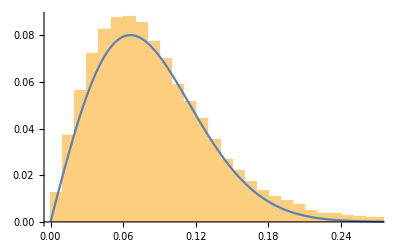

```mathematica
Clear["Global`*"]
dim=1000;
num=40;
mat=RandomVariate[GaussianOrthogonalMatrixDistribution[dim]];
λ=Eigenvalues[mat];
λ=Sort/@Eigenvalues/@RandomVariate[GaussianOrthogonalMatrixDistribution[dim],num];
λ[[All,2]]-λ[[All,1]];

res=Flatten[Transpose[λ[[All,#+1]]-λ[[All,#]]&/@Range[dim-1]]];
a=1;b=115;
P3[x_]:=2*x^a*Exp[-b*x^2]
Show[Histogram[res,{0.01},"Probability",PlotRange->Automatic],Plot[P3[x],{x,0,1},PlotRange->All] ]
```

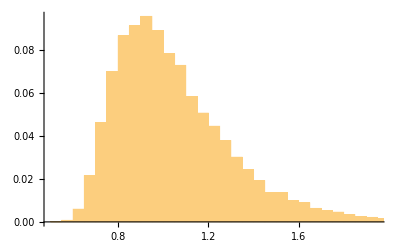

```mathematica
Clear["Global`*"]
dim=100;
num=20000;

λ=Sort/@Eigenvalues/@RandomVariate[GaussianOrthogonalMatrixDistribution[dim],num];

res=Max/@Transpose[λ[[All,#+1]]-λ[[All,#]]&/@Range[dim-1]];

a=9;b=5;
P3[x_]:=10*x^a*Exp[-b*x^2]

Show[Histogram[res,{0.05},"Probability",PlotRange->Automatic]]
```